## Certifying the non-existence of mono-unstable homogeneous convex polyhedra with fewer than 7 vertices

This Mathematica notebook is the source code accompanying the paper “The smallest mono-unstable, homogeneous convex polyhedron has at least 7 vertices.” by S. Bozóki, G. Domokos, D. Papp, and K. Regős.

This code was prepared by DP. You may direct questions to dpapp@ncsu.edu.

```mathematica
$Version
DateString[]
```

13.3.1 for Mac OS X ARM (64-bit) (July 24, 2023)

Tue 30 Jan 2024 13:55:17

### Auxiliary functions for manipulating polyhedral graphs and quadratic functions (runs automatically)

Throughout, combinatorial polyhedra are represented as a list of faces (“FaceList”), wherein each face is represented as a list of vertices.

```mathematica
(* Returns the list of edges of the polyhedron given by FaceList. *)
Edges[FaceList_]:=Union@@Table[Sort/@Subsets[f,{2}],{f,FaceList}]
```

```mathematica
(* Returns the tetrahedral decomposition of the polyhedron given by FaceList with respect to the vertex u. *)
(* The decomposition is represented as a list of tetrahedra (as lists of vertices). *)
TetrahedralDecomposition[FaceList_,u_]:=Prepend[#,u]&/@Select[FaceList,!MemberQ[#,u]&]
```

```mathematica
(* Returns a symmetric coefficient array for the not necessarily homogeneous quadratic polynomial quad wrt to the variables vars. *)
QArray[quad_,vars_]:=Block[{ca=Normal[CoefficientArrays[quad,vars,"Symmetric"->True]]},
If[Length[ca]==3,
ArrayFlatten[{{ca[[1]],{ca[[2]]/2}},{{ca[[2]]/2}ᵀ,ca[[3]]}}],
ArrayFlatten[{{ca[[1]],{ca[[2]]/2}},{{ca[[2]]/2}ᵀ,0}}]
]
]
```

### Generating the cases

```mathematica
(* The list of maximal polyhedral graphs with 5 or 6 vertices. *)
(* Note: the list is permuted to match the order in the paper. *)
Permute[Join@@Table[
Select[GraphData[V],GraphData[#,"Polyhedral"]&&Max[Length/@GraphData[#,"Faces"]]<=3&],
{V,{5,6}}
],{1,3,2}]

(* Face lists of the polyhedra. *)
Ps=GraphData[#,"Faces"]&/@%
```

{{Dipyramid,3},OctahedralGraph,{Hexahedral,5}}

{{{4,3,1},{1,3,5},{5,4,1},{2,3,4},{5,3,2},{2,4,5}},{{1,2,3},{4,2,1},{1,3,5},{5,4,1},{6,3,2},{2,4,6},{6,5,3},{4,5,6}},{{1,3,5},{6,3,1},{5,4,1},{1,4,6},{2,4,5},{6,4,2},{2,5,6},{6,5,3}}}

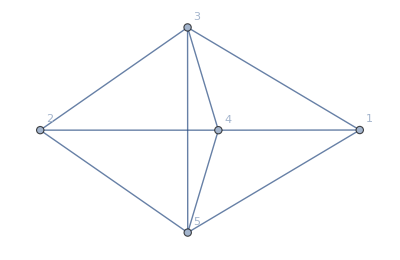
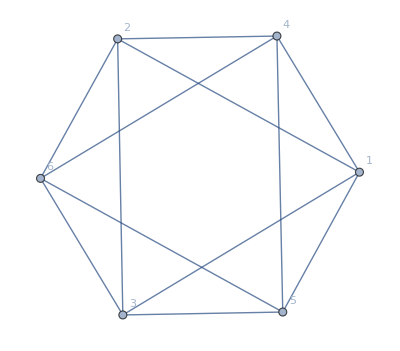
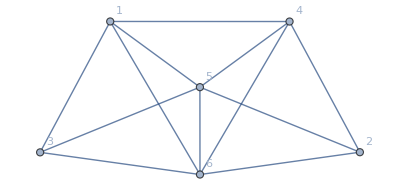

{PermutationGroup[{Cycles[{{4,5}}],Cycles[{{3,4}}],Cycles[{{1,2}}]}],PermutationGroup[{Cycles[{{3,4}}],Cycles[{{2,3},{4,5}}],Cycles[{{1,2},{5,6}}]}],PermutationGroup[{Cycles[{{5,6}}],Cycles[{{1,4},{2,3}}]}]}

```mathematica
(* Pictures and automorphism groups, to select representative vertices from each symmetric class of vertices *)
Graph[Edges[#],VertexLabels->"Name"]&/@Ps
GraphAutomorphismGroup[Edges[#]]&/@Ps
```

```mathematica
(* One representative vertex from each equivalence class (for each polyhedron). *)
(* For example: the dipyramid has two non-symmetric vertices, as 1 is equivalent with 2, and {3,4,5} form another equivalence class *)
us={{1,3},{1},{1,3,5}};
```

```mathematica
(* Generates and exports a table, in which each line corresponds to a case. *)
(* List of integers encoding the case: unstable vertex u, the remaining vertices Vs, the shadowing vertex j(i) for each i in Vs, and a single tetrahedron T from the tetrahedral decomposition. *)
cases=Flatten[
Table[
(* Next polyhedron to be processed and its graph. *)
P=Ps[[Pidx]];
G=Graph[Edges[P]];

(* Number of vertices. *)
V=Max[Flatten[P]];

(* the not-unstable vertices *)
Vs=Cases[Range[V],Except[u]];
(* Possible shadowing neighbors for each vertex in Vs *)
potentialShadows=Table[AdjacencyList[G,v],{v,Vs}];

(* Tetrahedral decomposition of P with respect to u. *)
Ts=TetrahedralDecomposition[P,u];

(* List of all possible shadowing relations (shadowing graphs) for the current polyhedron and candidate unstable vertex. *)
shadowMaps=Select[
Tuples[potentialShadows],
AcyclicGraphQ[Graph[Thread[DirectedEdge[Vs,#]]]]&
];

(* List of integers encoding the case: unstable vertex u, the remaining vertices Vs, the shadowing vertex j(i) for each i in Vs, and a single tetrahedron T from the tetrahedral decomposition. *)
Table[
Flatten[{u,Vs,s,T}],{s,shadowMaps},{T,Ts}
],
{Pidx,Length[Ps]},{u,us[[Pidx]]}],
3];

(* Save as CSV. *)
Export[NotebookDirectory[]<>"cases56.csv",cases,"CSV"];

(* Number of cases. *)
Length[cases]

(* Quick peek at the format. *)
cases
```

5943

### Generating infeasibility certificates

```mathematica
(* Load the list of cases. *)
cases=Import[NotebookDirectory[]<>"cases56.csv","CSV"];

(* Each line of the following table is a solution of the SDP corresponding to the case in the same line. *)
results=Table[
(* Parse the case line into suitable variables. Same notation as above. *)
V=(Length[case]-3)/2;
u=case[[1]];
Vs=case[[2;;V]];
s=case[[V+1;;2V-1]];
shadowMap=Thread[Vs->s];
T=case[[2V;;2V+3]];

(* Assemble the system of inequalities: shadowing relations and the center-of-mass inequality from T *)
shadowInequalities=Table[Sum[r[i,k]r[i/.shadowMap,k],{k,3}]-Sum[r[i,k]^2,{k,3}],{i,Vs}];
CoMInequalities={-Sum[r[i,1],{i,T}]};

(* WLOG, the candidate unstable vertex is at {1,0,0} *)
fix={r[u,1]->1,r[u,2|3]->0};
(* The complete system: quads >= 0 componentwise, with the coordinates of u substituted *)
quads=Join[shadowInequalities,CoMInequalities]/.fix;
vars=Variables[quads];

(* Set up and solve the semidefinite program. If z>0, the system is proven infeasible. *)
cs=Table[c[i],{i,Length[quads]}];
sol=Prepend[cs,z]/.SemidefiniteOptimization[-z,
And@@Thread[cs>=z]&&
VectorGreaterEqual[{Append[cs,1],0},"NormCone"]&&
VectorGreaterEqual[
{Sum[-cs[[i]]QArray[2quads[[i]],vars],{i,Length[quads]}],z IdentityMatrix[Length[vars]+1]},
{"SemidefiniteCone",Length[vars]+1}
]
,Prepend[cs,z],Method->"CSDP"]

,{case,cases}]

(* If this is sufficiently positive, we should be fine. *)
Min[First/@results]
```

0.00778495

### Verifying the certificates in rational arithmetic

```mathematica
(* Nearby rational y vectors for certificates as explained in the paper. *)
ys=Rationalize[Rest/@results,10^-8];
Min[Flatten[ys]]>0
```

True

```mathematica
verify=Table[
(* Parse the case line into suitable variables. Same notation as above, except to match the notation of the paper, the "quads" list represents nonpositive polynomials. *)
case=cases[[casenum]];
V=(Length[case]-3)/2;
u=case[[1]];
Vs=case[[2;;V]];
s=case[[V+1;;2V-1]];
shadowMap=Thread[Vs->s];
T=case[[2V;;2V+3]];

(* Assemble the system of inequalities: shadowing relations and the center-of-mass inequality from T *)
shadowInequalities=Table[Sum[r[i,k]r[i/.shadowMap,k],{k,3}]-Sum[r[i,k]^2,{k,3}],{i,Vs}];
CoMInequalities={-Sum[r[i,1],{i,T}]};

(* WLOG, the candidate unstable vertex is at {1,0,0} *)
fix={r[u,1]->1,r[u,2|3]->0};
(* The complete system: quads <= 0 componentwise, with the coordinates of u substituted *)
quads=-Join[shadowInequalities,CoMInequalities]/.fix;
vars=Variables[quads];

(* The rational certificate. *)
y=ys[[casenum]];
(* The conic combination of the quadratics. *)
f=quads.y;
(* Verify in exact arithmetic that the conic combination is strictly convex and that its unique minimum is positive. *)
{PositiveDefiniteMatrixQ[D[f,{vars,2}]],First[Minimize[f,vars]]>0}

,{casenum,Length[cases]}]

And@@Flatten[verify]
```

True